# Deuteron Transfer

```mathematica
m1H=938.272;
m3He=2808.391427;
m6Li=5601.518286;
m28Si=26053.187104;
m4He=3727.379188;
m30P=27916.95645;
```

```mathematica
Simplify[Solve[√(m1^2+p^2)+√(m2^2+p^2)==Ecm+m1+m2, p],{Ecm>0,Ecm+m1+m2>0}]
```

{{p→-(√(Ecm (Ecm+2 m2)) √((Ecm+2 m1) (Ecm+2 (m1+m2))))/(2 (Ecm+m1+m2))},{p→(√(Ecm (Ecm+2 m2)) √((Ecm+2 m1) (Ecm+2 (m1+m2))))/(2 (Ecm+m1+m2))}}

```mathematica
L[β_]:={{1/(√(1-β^2)),0,β/(√(1-β^2))},{0,1,0},{β/(√(1-β^2)),0,1/(√(1-β^2))}};
R[θ_]:={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
KE[A_,m_]:=A[[1]]-m
mass[A_]:=√(A[[1]]^2-Norm[A[[{2,3}]]]^2)
β[A_]:=A[[3]]/A[[1]]
PolarAngle[A_]:=ArcTan[A[[3]],A[[2]]]
```

```mathematica
(* rection A(B,2)1 *)
Transfer[mA_,mB_,m1_,m2_,A1_,A2_,T_,θNN_,Ex1_,Ex2_]:={
pA={mA,0,0};
pB={mB+T,0,√(2mB T+T^2)};
Q=mA+mB-m1-Ex1-m2-Ex2;
pc=(pA+pB)/2;
βc=pc[[3]]/pc[[1]];
pAc=L[-βc].pA;
pBc=L[-βc].pB;
Ecm=Q+pAc[[1]]-mA+pBc[[1]]-mB;
p=(√(Ecm (Ecm+2 (m2+Ex2))) √((Ecm+2 (m1+Ex1)) (Ecm+2 (m1+m2+Ex2+Ex1))))/(2 (Ecm+m1+m2+Ex1+Ex2));
p2c={√((m2+Ex2)^2+p^2),p Sin[θNN],p Cos[θNN]};
p1c={√((m1+Ex1)^2+p^2),-p Sin[θNN],-p Cos[θNN]};
p1=L[βc].p1c;
p2=L[βc].p2c;
pA,
pB,
{(p1[[1]]-m1)/A1,PolarAngle[p1]/Degree},
{(p2[[1]]-m2)/A2,PolarAngle[p2]/Degree}
}
```

```mathematica
Transfer[m6Li,m28Si,m4He,m30P,4,30,60 *28, 90 Degree,0,0]
{pA, pB,pAc,pBc,p1c,p2c,p1,p2}//TableForm
{m28Si+m6Li,m30P+m4He,m28Si+m6Li-m30P-m4He}
pA+pB-p1-p2
mass[p1]-m4He
```

{{5601.52,0,0},{27733.2,0,9505.85},{110.551,-50.4852},{41.6056,9.83388}}

5601.52 | 0 | 0
27733.2 | 0 | 9505.85
5844.18 | 0. | -1666.55
26106.4 | 0. | 1666.55
3996.46 | -1441.63 | 0.
27954.2 | 1441.63 | 0.
4169.58 | -1441.63 | 1189.01
29165.1 | 1441.63 | 8316.83

{31654.7,31644.3,10.3698}

{-3.63798×10^-12,0.,0.}

0.

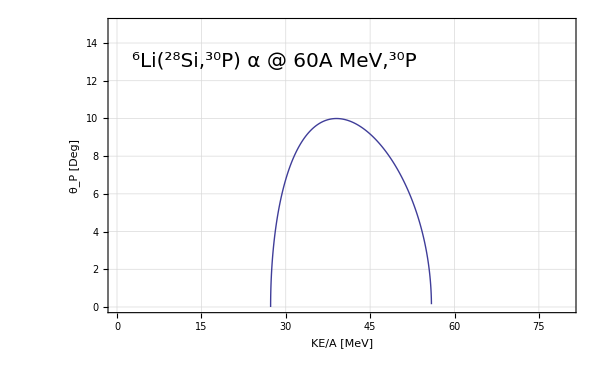

```mathematica
ListPlot[{
Table[Transfer[m6Li,m28Si,m4He,m30P,4,30,60 28,x Degree,0,0][[4]],{x,1,180,1}]
},PlotRange->{{0,80},{0,15}}, Frame->True,Joined->True,
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["KE/A [MeV]",14],Style[ "θ_P [Deg]",14]},
Epilog->Text[Style["^6Li(^28Si,^30P) α @ 60A MeV,^30P",20],{28,13},Background->White],ImageSize->600]
```

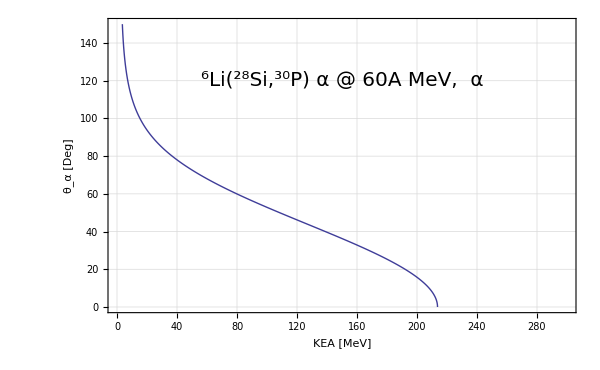

```mathematica
ListPlot[{
Table[Transfer[m6Li,m28Si,m4He,m30P,4,30,60 28,x Degree,0][[3]],{x,180,359,1}]
},PlotRange->{{0,300},{0,150}}, Frame->True,Joined->True,
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["KEA [MeV]",14],Style[ "θ_α [Deg]",14]},
Epilog->Text[Style["^6Li(^28Si,^30P) α @ 60A MeV,  α",20],{150,120},Background->White],ImageSize->600]
```

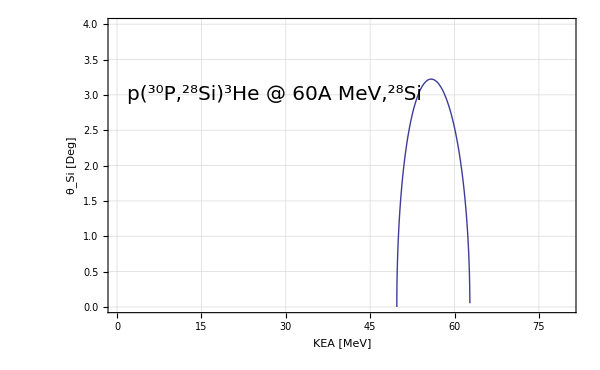

```mathematica
ListPlot[{
Table[Transfer[m1H,m30P,m3He,m28Si,3,28,60*30,x Degree][[4]],{x,1,180,1}]
},PlotRange->{{0,80},{0,4}}, Frame->True,Joined->True,
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["KEA [MeV]",14],Style[ "θ_Si [Deg]",14]},
Epilog->Text[Style[" p(^30P,^28Si)^3He @ 60A MeV,^28Si",20],{28,3},Background->White],ImageSize->600]
```

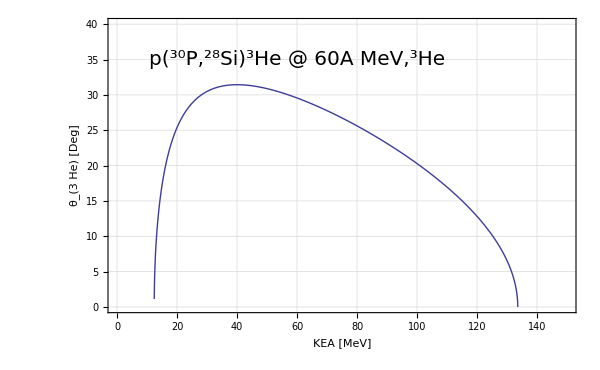

```mathematica
ListPlot[{
Table[Transfer[m1H,m30P,m3He,m28Si,3,28,60*30,x Degree][[3]],{x,180,359,1}]
},PlotRange->{{0,150},{0,40}}, Frame->True,Joined->True,
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameLabel->{Style["KEA [MeV]",14],Style[ "θ_(3  He) [Deg]",14]},
Epilog->Text[Style[" p(^30P,^28Si)^3He @ 60A MeV,^3He",20],{60,35},Background->White],ImageSize->600]
```